# Classify Critical Points

Author: Wenzhen Zhu
Created: Feb, 2014
Modified: July, 2014

## Project Description

An important problem in multivariable calculus is to find the extrema of a multivariable function. Extrema is the most basic feature of the graph of a function, includes maxima, minima, and saddle points. ClassifyCriticalPoints can find the critical points of a multivariable function and classify them.

## Functions

#### SelectReal

SelectReal[rules,vars] selects from the list of lists of rules whose rules involves only real numbers.

```mathematica
SelectReal[rules_List,vars_List]:= Select[rules, Element[vars/.#, Reals]&]
```

#### HessianMatrix

HessianMatrix[f,{vars}] computes the Hessian matrix of the function f with respect to the variables vars

```mathematica
HessianMatrix[f_,vars_]:= Outer[D[f, #1, #2]&, vars, vars]
```

#### ClassifyCriticalPoints

```mathematica
ClassifyCriticalPoints[fun_,vars_List]:=
	Module[{soln,hmat,hmatn,decide,detlist1,detlist2},
	soln = SelectReal[Solve[Thread[D[fun,#]&/@vars==Table[0,{Length[vars]}]],vars],vars];
	hmat = HessianMatrix[fun,vars];
	hmatn[x_]:= hmat[[1;;x,1;;x]];
	detlist1 = Table[Det[hmatn[i]],{i,1,Length[vars]}];
	detlist2 = Table[(-1)^i Det[hmatn[i]],{i,1,Length[vars]}];
	decide[detlist1_List,detlist2_List]:=
			If[And@@Map[N[#]>0&,detlist1]==True,"Local Minimum",
			If[And@@Map[N[#]>0&,detlist2]==True,"Local Maximum",
			If[Or@@Map[N[#]==0&,detlist1]==True,"Inconclusive",
			"Saddle Point"]]];	
	{decide[detlist1,detlist2],vars}/.soln
]
```

## Notes

This project was inspired when I was taking Multivariable Calculus class in my freshman year. An important problem in multivariable calculus is to find the extrema of a multivariable function.

### Here is how my professor introduced the necessary condition for extrema:

#### Stationary Point, Critical Point

A stationary point is a point where the gradient vanishes. A critical point is a stationary point or a point in the domain of the function where the gradient fails to exist.

#### Theorem

Suppose f is a differentiable function. If f has an extremum at an interior point (x_0,y_0) of its domain, then ∇f(x_0,y_0)=(0,0).

### The most usual way to classify critical points

Using the second derivative test to find the extrema:

Suppose that f has continuous second order partial derivatives and that f has a critical point at (x_0,y_0).

If ∂_(x x) f(x_0,y_0)∂_(y y) f(x_0,y_0)-(∂_(x y) f(x_0,y_0))^2>0 and ∂_(x x) f(x_0,y_0)>0, then f has a local min at (0,0).
If ∂_(x x) f(x_0,y_0)∂_(y y) f(x_0,y_0)-(∂_(x y) f(x_0,y_0))^2>0 and ∂_(x x) f(x_0,y_0)<0, then f has a local max at (0,0).
If ∂_(x x) f(x_0,y_0)∂_(y y) f(x_0,y_0)-(∂_(x y) f(x_0,y_0))^2<0, then (0,0) is a saddle point of f.

### A homework problem a Find and classify critical points

Find and classify the critical points of the function f(x,y)=8 x y √(1-x^2/4-y^2/9).

#### Solution:

The gradient of f is

```mathematica
Clear[f,gradf,x,y]
f[x_,y_]:=8 x y √(1-x^2/4-y^2/9)
gradf[x_,y_]=Grad[f[x,y],{x,y}]
```

{-(2 x^2 y)/(√(1-x^2/4-y^2/9))+8 y √(1-x^2/4-y^2/9),-(8 x y^2)/(9 √(1-x^2/4-y^2/9))+8 x √(1-x^2/4-y^2/9)}

The critical points are

```mathematica
cpts=Solve[gradf[x,y]=={0,0}]
```

{{x→0,y→0},{x→-2/(√3),y→-√3},{x→2/(√3),y→-√3},{x→-2/(√3),y→√3},{x→2/(√3),y→√3}}

```mathematica
pts={x,y}/.cpts
```

{{0,0},{-2/(√3),-√3},{2/(√3),-√3},{-2/(√3),√3},{2/(√3),√3}}

Here is a plot and a contour plot of the function together with the critical points.

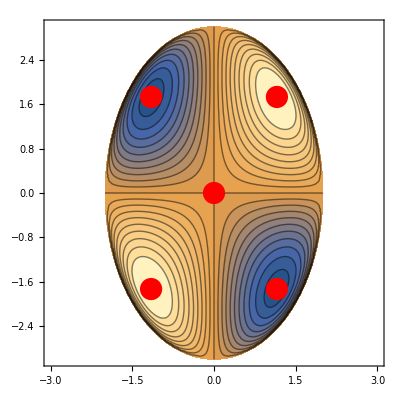

```mathematica
GraphicsRow[{Plot3D[f[x,y],{x,-3,3},{y,-3,3}],ContourPlot[f[x,y],{x,-3,3},{y,-3,3},Contours->20,Epilog->{Red,PointSize[0.04],Point/@pts}]}]
```

we can confirm with the second derivative test. First we compute the Hessian:

```mathematica
(hessian[x_,y_]=HessianMatrix[f[x,y],{x,y}])//MatrixForm
```

(-(x^3 y)/(2 (1-x^2/4-y^2/9)^(3/2))-(6 x y)/(√(1-x^2/4-y^2/9)) | -(2 x^2 y^2)/(9 (1-x^2/4-y^2/9)^(3/2))-(2 x^2)/(√(1-x^2/4-y^2/9))-(8 y^2)/(9 √(1-x^2/4-y^2/9))+8 √(1-x^2/4-y^2/9)
-(2 x^2 y^2)/(9 (1-x^2/4-y^2/9)^(3/2))-(2 x^2)/(√(1-x^2/4-y^2/9))-(8 y^2)/(9 √(1-x^2/4-y^2/9))+8 √(1-x^2/4-y^2/9) | -(8 x y^3)/(81 (1-x^2/4-y^2/9)^(3/2))-(8 x y)/(3 √(1-x^2/4-y^2/9)))

Evaluating the Hessian at the critical point we obtain

```mathematica
hcpts=hessian[x,y]/.cpts
```

{{{0,8},{8,0}},{{-16 √3,-16/(√3)},{-16/(√3),-64/(3 √3)}},{{16 √3,-16/(√3)},{-16/(√3),64/(3 √3)}},{{16 √3,-16/(√3)},{-16/(√3),64/(3 √3)}},{{-16 √3,-16/(√3)},{-16/(√3),-64/(3 √3)}}}

```mathematica
Map[MatrixForm,hcpts]
```

{(0 | 8
8 | 0),(-16 √3 | -16/(√3)
-16/(√3) | -64/(3 √3)),(16 √3 | -16/(√3)
-16/(√3) | 64/(3 √3)),(16 √3 | -16/(√3)
-16/(√3) | 64/(3 √3)),(-16 √3 | -16/(√3)
-16/(√3) | -64/(3 √3))}

```mathematica
Map[Det,hcpts]
```

{-64,256,256,256,256}

So the first critical point is saddle point, and max or min are the rest three. Examining the elements in the first row and column of the Hessian matrices we see that the second and the last one are max, and the third one and fourth one are min

At first, I solve this extrema kind of problems based on above procedure. After I took linear algebra and vector calculus, I wrote the following function, which is to generalize it to work for n-variables function.

```mathematica
ClassifyCriticalPoints[f[x,y],{x,y}]
```

{{Inconclusive,{0,0}},{Local Maximum,{-2/(√3),-√3}},{Local Minimum,{2/(√3),-√3}},{Local Minimum,{-2/(√3),√3}},{Local Maximum,{2/(√3),√3}}}

### Test

```mathematica
Clear[f,x,y,z]
f[x_,y_,z_]:=x^4+y^4+z^4-4 x y z
```

```mathematica
ClassifyCriticalPoints[f[x,y,z],{x,y,z}]
```

{{Local Minimum,{-1,-1,1}},{Local Minimum,{-1,1,-1}},{Inconclusive,{0,0,0}},{Local Minimum,{1,-1,-1}},{Local Minimum,{1,1,1}}}

## Source

Definition, theorem and problem are from my advisor Dennis Schneider’s mulitivariable calculus textbook. It is not officially published.